```mathematica
Needs["NumericalCalculus`"]
$Assumptions={Element[{ω, B, T, b},Reals]};
XROT[θ_] := XROT[θ] = Cos[ θ/2]*PauliMatrix[4] - ⅈ*Sin[θ/2]*PauliMatrix[1];
Theta[t2_,t1_, ω_]:= Sin[ω*t2]/ω - Sin[ω*t1]/ω;
U[t2_, t1_, b_, ω_] := Cos[b*Theta[t2, t1, ω]]*PauliMatrix[4] - ⅈ*Sin[b*Theta[t2, t1, ω]]*PauliMatrix[3];
Dagger[X_] := Refine[Conjugate[Transpose[X]], {θ ∈ Reals, ω ∈ Reals}];
(* We'll assume everything is equally spaced, this is technically wlog since you can alwayas consider a longer sequence...*)
(* Produces the associated Z string unitary on the jth pulse*)
rhoT[n_, t_, θ_, b_?NumericQ, ω_] :=   Module[{},
rtn = PauliMatrix[4];
For[i=1,i<n + 1,i++,
rtn=XROT[ θ].U[t/n*(i), t/n*(i-1), b, ω].rtn//N;];
rtn]
```

```mathematica
b0=1;
InnProd[t_, k_, ω_?NumericQ]:=Module[{},
ϕ=1/Sqrt[2]*(ND[rhoT[t*2^k, t, π/(2^k), b, ω].{{1},{1}}, b, b0])//N;
ψ = 1/Sqrt[2]*rhoT[t*2^k, t, π/(2^k), b0, ω].{{1},{1}};
4*((ConjugateTranspose[ϕ].ϕ)[[1]][[1]] + ((ConjugateTranspose[ψ].ϕ)[[1]][[1]])^2)]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Part::partd: Part specification 0.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 6.27918⟦1⟧ is longer than depth of object.

Part::partd: Part specification 12.5464⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {5.86065}. NIntegrate obtained 24.984 and 8.68851 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {10.0498}. NIntegrate obtained 31.1723 and 0.0934905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {41.0079}. NIntegrate obtained 37.6078 and 0.00330135 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{0.,6.27918,12.5464,18.8136,24.984,31.1723,37.6078,43.8512,50.0537,51.7537,57.859},{0.,4.51956,8.41023,11.441,17.4644,19.4332,23.3656,32.3421,32.856,41.9516,43.5074},{0.,4.48566,7.73243,10.1779,14.7723,21.5378,20.0652,22.5848,30.7441,32.6676,39.4184}}

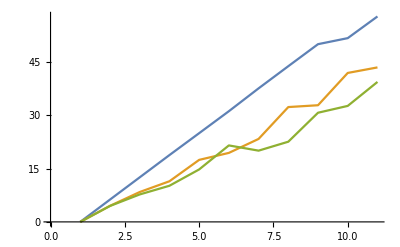

```mathematica
a = Table[Table[Re[NIntegrate[InnProd[T, j, ω], {ω, 0, 500}]][[1]][[1]],{T, 0, 10}], {j, 0,2}]
ListLinePlot[a]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Part::partd: Part specification 0.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 6.26327⟦1⟧ is longer than depth of object.

Part::partd: Part specification 12.4669⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.17839}. NIntegrate obtained 16.1901+9.05545×10^-9 ⅈ and 0.132655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.924395}. NIntegrate obtained 24.3656+5.0187×10^-8 ⅈ and 0.416907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.86915}. NIntegrate obtained 33.066+1.70164×10^-7 ⅈ and 1.43664 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{0.,6.26327,12.4669,18.6705,24.8742,31.0778,37.2814,43.4851,49.6887,55.8924,62.096},{0.,4.93323,10.4851,16.1901,24.3656,33.066,41.5621,51.906,58.7085,71.3584,85.7203},{0.,4.70892,11.2638,19.0153,29.3214,40.0988,54.6953,69.4073,85.955,106.146,127.08}}

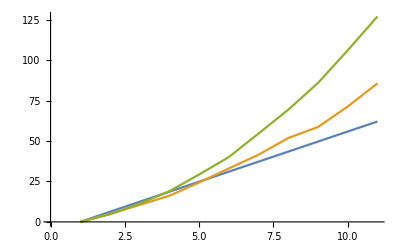

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Part::partd: Part specification 0.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 6.26327⟦1⟧ is longer than depth of object.

Part::partd: Part specification 12.4669⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {7.0297}. NIntegrate obtained 7.59083+5.07985×10^-10 ⅈ and 0.133898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.51408}. NIntegrate obtained 11.7492-1.04748×10^-9 ⅈ and 0.869722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.51408}. NIntegrate obtained 16.4615-1.67488×10^-8 ⅈ and 1.92629 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{0.,6.26327,12.4669,18.6705,24.8742,31.0778,37.2814,43.4851,49.6887,55.8924,62.096},{0.,4.64982,7.59083,11.7492,16.4615,18.0435,23.4141,27.6786,37.2697,41.2485,42.9826},{0.,4.57905,8.77091,10.126,14.1915,17.1086,20.799,26.8804,29.072,35.7711,35.0978}}

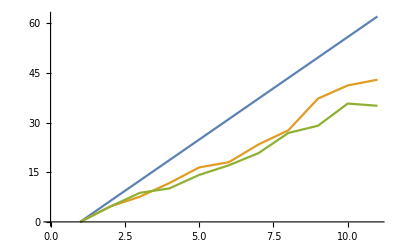

```mathematica
b0=10;
InnProd[t_, k_, ω_?NumericQ]:=Module[{},
ϕ=1/Sqrt[2]*(ND[rhoT[t*2^k, t, π/(2^k), b, ω].{{1},{1}}, b, b0])//N;
ψ = 1/Sqrt[2]*rhoT[t*2^k, t, π/(2^k), b0, ω].{{1},{1}};
4*((ConjugateTranspose[ϕ].ϕ)[[1]][[1]] + ((ConjugateTranspose[ψ].ϕ)[[1]][[1]])^2)]
a = Table[Table[Re[NIntegrate[InnProd[T, j, ω], {ω, 0, 100}]][[1]][[1]],{T, 0, 10}], {j, 0,2}]
ListLinePlot[a]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Part::partd: Part specification 0.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 6.28118⟦1⟧ is longer than depth of object.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {17.2559}. NIntegrate obtained 12.5585 and 0.00345271 for the integral and error estimates.

Part::partd: Part specification 12.5585⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {66.3907}. NIntegrate obtained 18.8285 and 0.000712736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {66.3907}. NIntegrate obtained 25.1156 and 0.00754769 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{0.,6.28118,12.5585,18.8285,25.1156,31.3544,37.4054,43.5415,49.8409,56.1409,60.7298},{0.,4.84559,8.31766,12.1772,19.6576,24.2201,23.543,25.6617,32.2333,34.4464,41.1447},{0.,4.53818,8.12513,12.0384,14.7206,22.3936,22.7437,27.5828,25.9109,35.5499,45.453}}

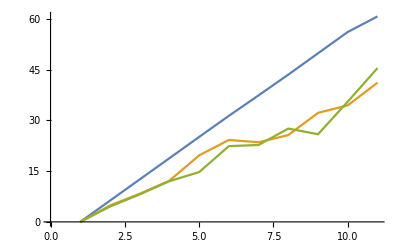

```mathematica
b0=100;
InnProd[t_, k_, ω_?NumericQ]:=Module[{},
ϕ=1/Sqrt[2]*(ND[rhoT[t*2^k, t, π/(2^k), b, ω].{{1},{1}}, b, b0])//N;
ψ = 1/Sqrt[2]*rhoT[t*2^k, t, π/(2^k), b0, ω].{{1},{1}};
4*((ConjugateTranspose[ϕ].ϕ)[[1]][[1]] + ((ConjugateTranspose[ψ].ϕ)[[1]][[1]])^2)]
a = Table[Table[Re[NIntegrate[InnProd[T, j, ω], {ω, 0, 1000}]][[1]][[1]],{T, 0, 10}], {j, 0,2}]
ListLinePlot[a]
```

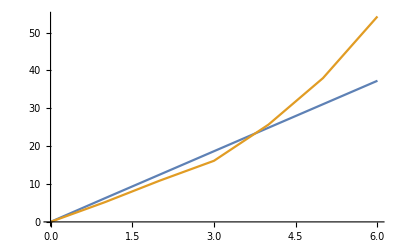

```mathematica
ListLinePlot[{a[[1]][[1;;7]], a[[2]][[1;;7]]}, DataRange->{0, 6}]
```

```mathematica
a[[1]][[1;;7]]
```

{0.,6.26327,12.4669,18.6705,24.8742,31.0778,37.2814}

```mathematica
Fit[a[[1]][[2;;20]],{1, x, x^2},x]
```

0.0542059+6.20678 x-0.000283761 x^2

```mathematica
Fit[a[[2]][[2;;20]],{1, x, x^2, x^3},x]
```

3.39599+0.680089 x+1.27562 x^2+0.000255543 x^3

```mathematica
data = Table[{i, a[[1]][[i+1]]}, {i, 0, 20}];
Fit[data,{1, x, x^2},x]
```

0.040697+6.20793 x-0.000267078 x^2

```mathematica
data = Table[{i, a[[2]][[i+1]]}, {i, 0, 20}];
```

```mathematica
curve = Fit[data,{1, x, x^2},x]
```

2.89648+0.575532 x+1.29192 x^2

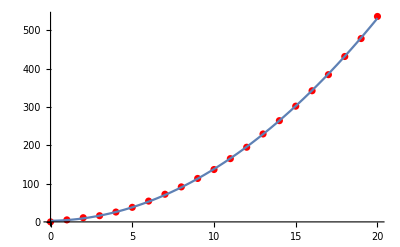

```mathematica
Show[ListPlot[data, PlotStyle->Red], Plot[curve, {x, 0, 20}]]
```

```mathematica
a[[2]][[1]]
```

0.

```mathematica
curve
```

1.14014 x+1.26896 x^2